NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273492-0.00214368 ⅈ and 0.0243771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0027378-0.00294045 ⅈ and 0.034719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.03855×10^-7-0.000538534 ⅈ and 0.0047202 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

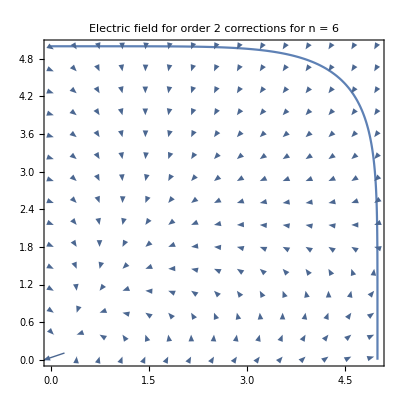

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.21834×10^-6-0.000459109 ⅈ and 0.0478578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.98249×10^-6-0.00243917 ⅈ and 0.0668455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.26921×10^-7-0.00046044 ⅈ and 0.00665807 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

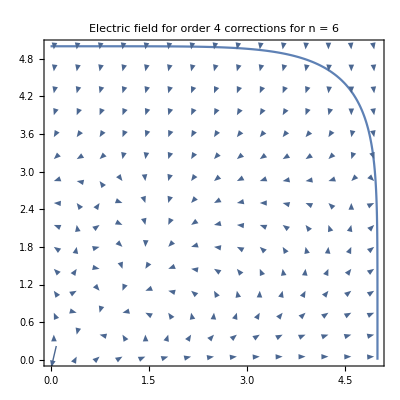

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00215053+7.83295×10^-6 ⅈ and 0.0255906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00338266+0.0000122937 ⅈ and 0.0478505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 4.40538×10^-7-0.000356909 ⅈ and 0.0215196 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

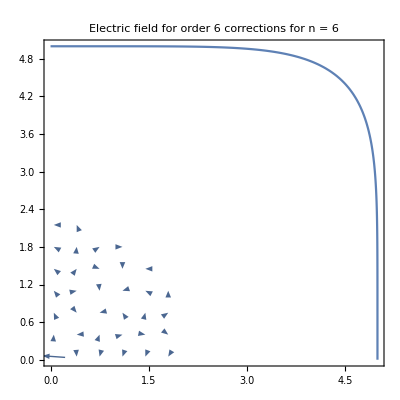

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -2.64961×10^-7+0.000139417 ⅈ and 0.00982937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained -1.52065×10^-7+0.000417443 ⅈ and 0.0366989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00215053+7.83295×10^-6 ⅈ and 0.0255906 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

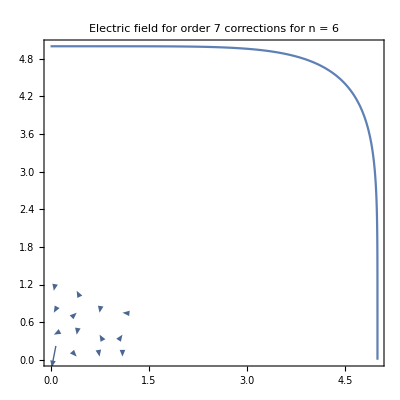

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=7;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0027349-0.00213827 ⅈ and 0.0243529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273781-0.00294292 ⅈ and 0.0328398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.04217×10^-7-0.000537646 ⅈ and 0.00469276 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

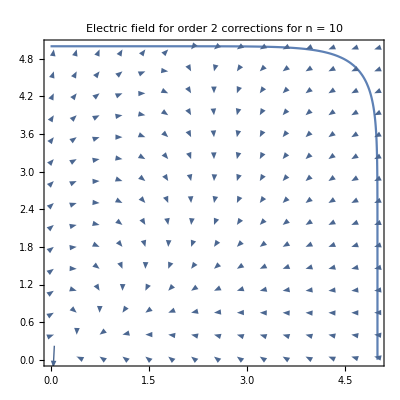

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=10;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.40139×10^-6-0.000449767 ⅈ and 0.0468563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 8.04831×10^-6-0.00244521 ⅈ and 0.0701628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.24982×10^-7-0.000458923 ⅈ and 0.00656837 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

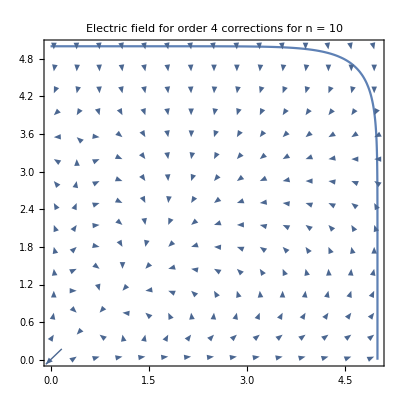

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=10;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00214596+7.81617×10^-6 ⅈ and 0.0250116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.81101×10^-6+4.44089×10^-16 ⅈ and 0.0968544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.85494×10^-8-0.000162259 ⅈ and 0.00827251 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

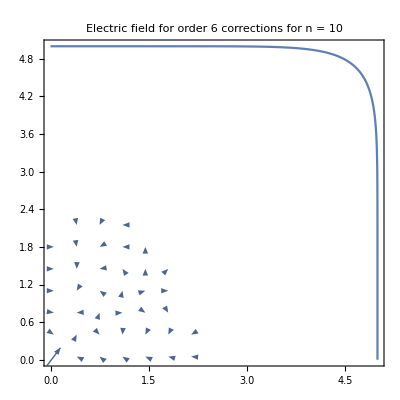

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=10;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.40688×10^-6-0.000449582 ⅈ and 0.0467025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 8.05006×10^-6-0.00244532 ⅈ and 0.0717088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.24932×10^-7-0.000458896 ⅈ and 0.00656037 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

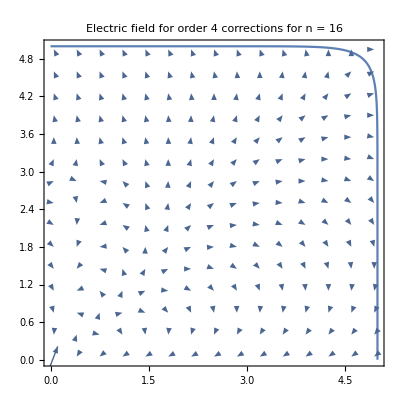

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=16;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00214588+7.81588×10^-6 ⅈ and 0.0256441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.81512×10^-6+6.10623×10^-16 ⅈ and 0.099826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.8436×10^-8-0.000162244 ⅈ and 0.00822518 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

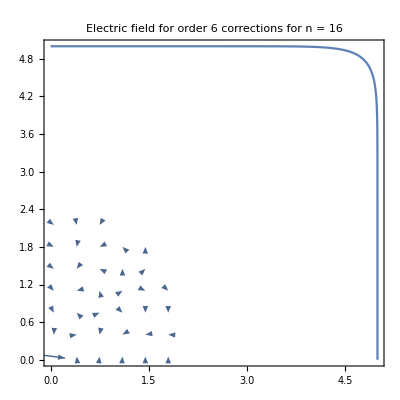

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=16;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.40691×10^-6-0.000449581 ⅈ and 0.0467016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 8.05006×10^-6-0.00244532 ⅈ and 0.072155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.24932×10^-7-0.000458896 ⅈ and 0.00656312 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

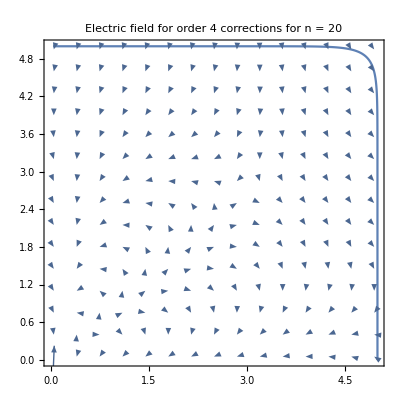

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=20;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.40691×10^-6-0.000449581 ⅈ and 0.046775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 8.05006×10^-6-0.00244532 ⅈ and 0.0730779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.24932×10^-7-0.000458896 ⅈ and 0.00657862 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

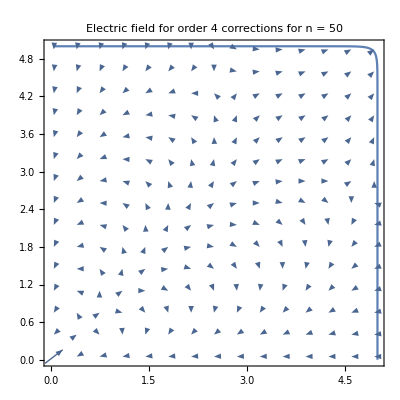

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=50;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -2.08222×10^-6+1.2837×10^-16 ⅈ and 0.0475425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.81514×10^-6+1.66533×10^-16 ⅈ and 0.102516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.84354×10^-8-0.000162244 ⅈ and 0.00823874 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

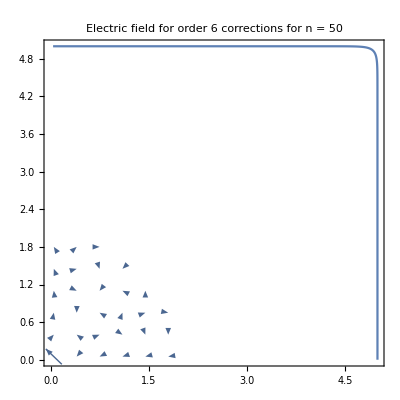

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=50;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -2.08222×10^-6+1.04083×10^-16 ⅈ and 0.0475559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 3.81514×10^-6+3.88578×10^-16 ⅈ and 0.102901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.84354×10^-8-0.000162244 ⅈ and 0.00824677 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

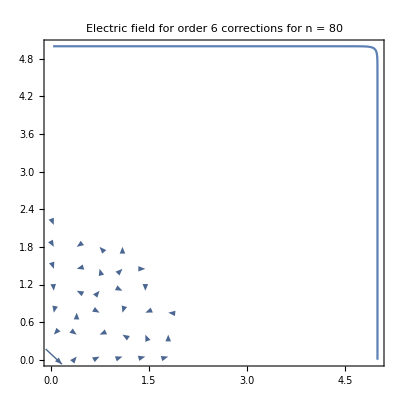

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=80;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2.01}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```